```mathematica
Directory[]
```

/Users/alexis/workspace/clustersearch/cpp/build

```mathematica
SetDirectory["/Users/alexis/workspace/clustersearch/cpp/build"]
```

/Users/alexis/workspace/clustersearch/cpp/build

```mathematica
Clusters[alpha_,length_,colors_,gray_,samples_]:=
(* Returns means of cluster_size, perimeter_size, colors, exits_size, robustness *)
Block[{args,command,seed=0},
args="";
args = StringJoin[args," ", "--alpha=",     ToString[alpha]];
args = StringJoin[args," ", "--length=",   ToString[length]];
args = StringJoin[args," ", "--colors=",   ToString[colors]];
args = StringJoin[args," ", "--gray=",       ToString[gray]];
args = StringJoin[args," ", "--samples=", ToString[samples]];
args = StringJoin[args," ", "--seed=",       ToString[seed]];
args = StringJoin[args," ", "--verbose=0"];
command=StringJoin["!./clusters",args];
Flatten @ ReadList[command,Number,RecordLists->True]]
```

```mathematica
Clusters[2,10,4,0,1]
```

{240,691,3,1718,0.284167}

```mathematica
(* Headings of Clusters output, for labelling tabular displays.

For example:
 TableForm[<output>,TableHeadings->{None,ClustersHeadingsShort},TableAlignments->"."];
   Grid[%129~Prepend~ClustersHeadingsShort,Alignment->"."];
 *)
ClustersHeadingsShort=
{"s","t","E","u","r"};
ClustersHeadingsLong={"cluster_size","perimeter_size","colors_seen","exits_size","robustness"};
```

Suppose that I want to
hold constant
   alpha =2
   length=10 
   samples = 15
   gray=0

let 
  colors range from 2 to 5,
 
and generate a table of  outputs from Clusters

```mathematica
(* Generate table ranging over colors from 2..5 *)
With[{alpha=2,length=8,samples=100,gray=0},
Table[Clusters[alpha,length,colors,gray,samples],{colors,2,5}]]
```

{{126.58,125.85,1,503.58,0.496301},{74.45,148.44,2,386.32,0.325612},{38.43,112.36,2.99,215.6,0.237349},{15.93,62.35,3.96,93.76,0.191666}}

Display it as a table with headings

```mathematica
ClustersTableForm[table_]:=
TableForm[table,TableHeadings->{None,ClustersHeadingsShort},TableAlignments->"."]
```

```mathematica
ClustersTableForm[%129]
```

s | t | E | u | r
126.58 | 125.85 | 1 | 503.58 | 0.496301
74.45 | 148.44 | 2 | 386.32 | 0.325612
38.43 | 112.36 | 2.99 | 215.6 | 0.237349
15.93 | 62.35 | 3.96 | 93.76 | 0.191666

Suppose I want to generate the same table as below, but left-joining a column of colors

```mathematica
(* Generate table ranging over colors from 2..5 *)
With[{alpha=2,length=8,samples=10,gray=0},
Table[{colors}~Join~Clusters[alpha,length,colors,gray,samples],{colors,2,5}]]
```

{{2,126.9,127.7,1,508,0.497934},{3,66.6,132.9,2,347.4,0.294298},{4,44.6,126.6,3,245.4,0.272793},{5,19.1,70.2,3.9,111.2,0.175014}}

Display it as a table with headings, adding a new heading m for colors allowed.

```mathematica
RangingClustersTableForm[table_,rangeHeader_]:=
(* Clusters output, with a ranging input var in left col *)
TableForm[table,
TableHeadings->{None,{rangeHeader}~Join~ClustersHeadingsShort},
TableAlignments->"."]
```

```mathematica
RangingClustersTableForm[%171,"m"]
```

m | s | t | E | u | r
2 | 126.9 | 127.7 | 1 | 508 | 0.497934
3 | 66.6 | 132.9 | 2 | 347.4 | 0.294298
4 | 44.6 | 126.6 | 3 | 245.4 | 0.272793
5 | 19.1 | 70.2 | 3.9 | 111.2 | 0.175014

```mathematica
PickColumn1andCol[table_,col]:=
(* Picks cols 1 and COL from table *)
Map[( #[[{1,col}]] & ),table]
```

```mathematica
PickColumn1andColumnX[%171,6]
```

{{2,0.497934},{3,0.294298},{4,0.272793},{5,0.175014}}

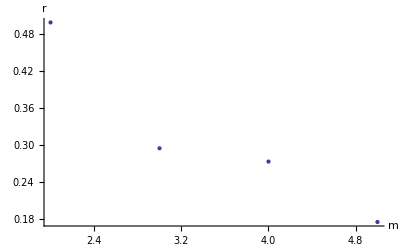

```mathematica
ListPlot[%191,AxesLabel->{m,r}]
```